```mathematica
u0=1.*10^-8;α=0.1;a=0.1;V[r_]=-α/r;δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
Veff[c_,d_][r_]=-α/r Erf[r/(√2 a)]+c a^2 δa[r]+d a^4(-(3 ⅇ^(-r^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-r^2/(2 a^2)) r^2)/(2 √2 a^7 π^(3/2)));
m=1.;l=0;l1=-1/2+√((l+1/2)^2-(α)^2);
k:=√((e+m)^2-m^2);γ:=(*(√(k^2+m^2) α)/k*)(α m)/k;
r2=u0;
r1=50.;
re=1000.;
```

```mathematica
WList={10^-10,10^-5,.001,.003,.007,.01,.03,.07,.1,.3,.7,1};
```

```mathematica
Realva={0.15371513493592534,0.9244866810902964,-0.2878351571737228,0.25528639785855345,0.31741138754732695,0.3042488534914061,0.22048729085688354,0.15819049712226996,0.13705446724918247,0.09139840763169624,0.0726746912976126,0.06795477378987547};
Realva1={1.57062958127295,1.5171948969734057,0.7194917913962204,-0.017173843767820635,-0.657690842396933,-0.8971099931274864,-1.5611169827353257,1.198673864385493,1.0719675950305827,0.7990978539377087,0.6974056234372554,0.6790303670126097};
Realen={0.005063846994876053,0.0012603372008835878,0.0005588472250714904,0.0003139365491734436,0.00020075015284415354,0.0001393286361501822,0.0001023202692626013,0.00007831347958375812,0.00006186146208497778,0.00005009740892103487,0.0000413957463856196,0.00003477894262660097,0.000029630516582668243,0.000025546080086868983,0.000022251441779141956,0.000019555362955836486,0.0000173211682396035,0.00001544907710193666,0.000013864867079216303,0.000012512402293718417};
```

```mathematica
Clear[e,c,d,sol1]
```

```mathematica
sol1=First@ParametricNDSolve[{-f''[x]+2m Veff[c,d][x]f[x]-(e-Veff[c,d][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},{e,c,d},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50]
```

f→ParametricFunction[<>]

```mathematica
FindRoot[{Block[{e=10^-10},(temp1=((f[e,c,d]'[r1] ((e-Veff[c,d][r1])/(8 m)+1)-(f[e,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(e-Veff[c,d][r1])/(8m))f[e,c,d][r1])-(k+γ/r1)  Cot[k r1+Realva1[[1]]])/.sol1)==0],Block[{e=10^-5},(temp2=((f[e,c,d]'[r1] ((e-Veff[c,d][r1])/(8 m)+1)-(f[e,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(e-Veff[c,d][r1])/(8m))f[e,c,d][r1])-(k+γ/r1)  Cot[k r1+Realva1[[2]]])/.sol1)==0]}(*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*),{{c,2},{d,11}},MaxIterations->10000,AccuracyGoal->8,WorkingPrecision->30,StepMonitor:>Print[N[{c,d},10],{temp1,temp2}]]
```

FindRoot::precw: 参数函数的精度 ({0.0764186  + (1 + Times[« 2 »])\ SuperscriptBox[TagBox[ParametricFunction[« 6 »], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 3 »], "′", Rule[MultilineFunction, None]][50.] - 0.125\ « 1 »\ TagBox[ParametricFunction[1, Internal`Bag[StyleBox["\"<\"", Rule[ShowStringCharacters, False]]  1  StyleBox["\">\"", Rule[ShowStringCharacters, False]]], 1, 1, {« 6 »}, {« 2 »}], False, Rule[Editable, False], Rule[SelectWithContents, True]][« 1 »][50.]/(1 + 0.125\ Plus[« 3 »])\ TagBox[ParametricFunction[1, « 4 », {NDSolve`base$673867, NDSolve`NDSolveParametricFunction[« 10 »]}], False, Rule[Editable, False], Rule[SelectWithContents, True]][1/1 « 8 » 00, c, d][50.] == 0, « 20 »  + « 1 »/« 1 » == 0}) 小于 WorkingPrecision (30.).

{-8.082007159,4.165249718}{0.000194295,0.000199902}

{-11.80563637,0.7597067414}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80564432,0.759697446}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80565228,0.7596881505}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80566024,0.7596788551}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80566819,0.7596695596}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80567615,0.7596602641}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80568411,0.7596509687}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80569206,0.7596416732}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80570002,0.7596323777}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80570798,0.7596230822}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80571593,0.7596137867}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80572389,0.7596044912}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80573185,0.7595951957}{-8.49479×10^-6,-6.1852×10^-6}

{-11.8057398,0.7595859001}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80574776,0.7595766046}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80575572,0.759567309}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80576367,0.7595580135}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80577163,0.7595487179}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80577959,0.7595394223}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80578754,0.7595301267}{-8.49479×10^-6,-6.1852×10^-6}

{-11.8057955,0.7595208311}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80580346,0.7595115355}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80581141,0.7595022399}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80581937,0.7594929443}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80582733,0.7594836487}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80583528,0.759474353}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80584324,0.7594650574}{-8.49479×10^-6,-6.1852×10^-6}

{-11.8058512,0.7594557617}{-8.49479×10^-6,-6.1852×10^-6}

{-11.80585915,0.7594464661}{-8.49479×10^-6,-6.1852×10^-6}

$Aborted

```mathematica
{c,d}={-13.08167178900705614669898613748098962809`10.,-0.86757872505378829326232208985975874744`10.};(*Worst, worse than c*)
```

```mathematica
{c,d}={12.09222397195114375706440732334329830914`10.,17.82490139712165044377705825248754971776`10.};(*a little better than c*)
```

```mathematica
{c,d}={1.41612097317324664088391252386085243384`10.,11.54265441370668878380943906983901230501`10.};(*ps better,energy not good*)
```

```mathematica
(f[e,c,d]'[r1] ((e-Veff[c,d][r1])/(8 m)+1)-(f[e,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(e-Veff[c,d][r1])/(8m))f[e,c,d][r1])-(k+γ/r1) Cot[k r1+Realva1[[1]]]/.sol1/.e->10^-10
```

-5.11165×10^-6

```mathematica
Flatten@Map[{
e=#;
sol1=First@NDSolve[{-f''[x]+2m Veff[c,d][x]f[x]-(e-Veff[c,d][x])^2/4 f[x]==2m e f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{f[r2]==u0,f'[r2]==1}}];
δs1=FindRoot[(f'[r1] ((e-Veff[c,d][r1])/(8 m)+1)-(f[r1] Veff[c,d]'[r1])/(8 m))/((1+(e-Veff[c,d][r1])/(8m))f[r1])==(k+γ/r1) Cot[k r1+δ](*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+δ]*)/.sol1,{δ,-0.5}]; 
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&]}&,WList]
```

NDSolve::precw: 参数函数的精度 ({2.` (0.8991466950950516` Power[« 2 »] + 0.0011542654413706694` Plus[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (1/10000000000 + Times[« 2 »] + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({2.` (0.8991466950950516` Power[« 2 »] + 0.0011542654413706694` Plus[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (1/100000 + Times[« 2 »] + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({2.` (0.8991466950950516` Power[« 2 »] + 0.0011542654413706694` Plus[« 2 »] - 0.1` Power[« 2 »] Erf[« 1 »]) f[x] - 1/4 (0.001`  + Times[« 2 »] + Times[« 2 »] + Times[« 3 »])^2 f[x] - SuperscriptBox[{}{}{}{}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve :: precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

{1.57063,1.51719,0.717513,-0.0226381,-0.6728,-0.919802,1.49348,0.926182,0.616579,-1.39027,-0.23318,1.52748}

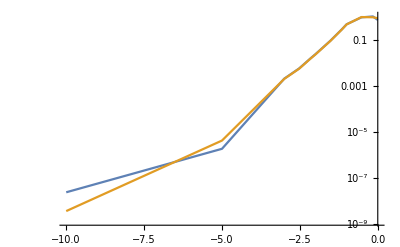

```mathematica
ListLogPlot[{Transpose[{Log10@WList,Min[#]&/@Transpose[{Mod[cList-Realva1,π],π-Mod[cList-Realva1,π]}]}],Transpose[{Log10@WList,Min[#]&/@Transpose[{Mod[%23-Realva1,π],π-Mod[%23-Realva1,π]}]}]},Joined->True(*,PlotRange->{{0,7},{10^-3,-10^-2}}*),PlotRange->All]
```

```mathematica
cList={1.5706296048779658,1.517196718765972,0.7174678845311157,-0.022785841296686978,-0.6731737496738939,-0.9203482711531734,1.491731702275432,0.9216031049397442,0.6096635448023283,-1.4175387958007049,-0.31287125601735105,1.3908394493539582};
```

```mathematica
Clear[e]
```

```mathematica
re=15000.;
```

```mathematica
sol2=ParametricNDSolve[{-f''[x]+2m Veff[c,d][x]f[x]-(e-Veff[c,d][x])^2/4 f[x]==2m e f[x],f[re]==u0,f'[re]==-u0},f,{x,re,r2},e,PrecisionGoal->10,MaxStepFraction->10^-3/2,MaxSteps->Infinity]
```

{f→ParametricFunction[<>]}

```mathematica
Realen
```

{0.00506385,0.00126034,0.000558847,0.000313937,0.00020075,0.000139329,0.00010232,0.0000783135,0.0000618615,0.0000500974,0.0000413957,0.0000347789,0.0000296305,0.0000255461,0.0000222514,0.0000195554,0.0000173212,0.0000154491,0.0000138649,0.0000125124}

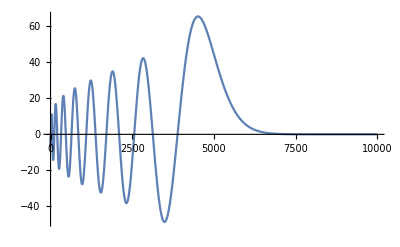

```mathematica
Plot[f[-0.00002][r]/.sol2,{r,0,10000},PlotRange->All]
```

```mathematica
FindRoot[f[e][r2]==0/.sol2,{e,-0.000017,-0.000018},PrecisionGoal->8,StepMonitor:>Print[e,{f[e][r2]/.sol2}]]
```

-0.000017{-9.56466×10^16}

-0.0000170099{-9.6729×10^16}

-0.0000170099{-9.6729×10^16}

-0.0000171003{-1.00763×10^17}

-0.0000173026{-1.84184×10^16}

-0.0000173026{-1.84184×10^16}

-0.0000173186{-1.62591×10^15}

-0.0000173201{1.45165×10^13}

-0.0000173201{-8.4612×10^10}

-0.0000173201{-1.97172×10^8}

-0.0000173201{-1.97172×10^8}

-0.0000173201{-5.20187×10^6}

-0.0000173201{-5.20187×10^6}

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→-0.0000173201}

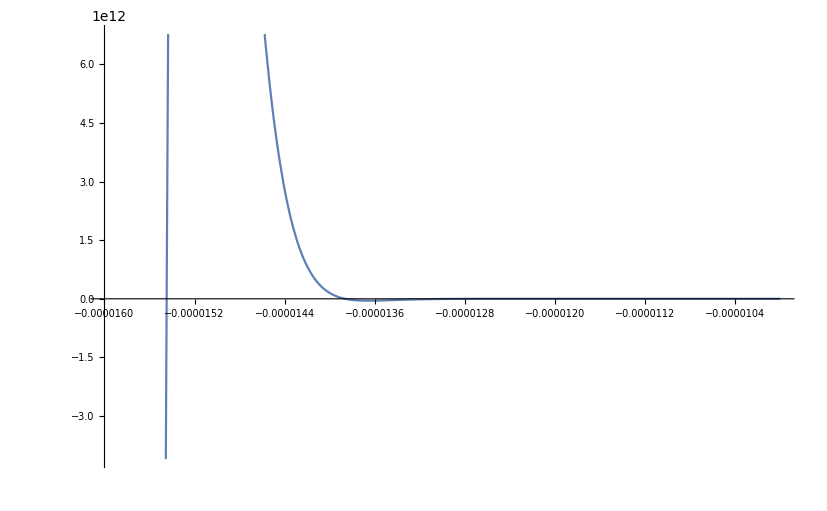

```mathematica
Plot[f[e][r2]/.sol2,{e,-0.00001,-0.000016}]
```

```mathematica
1/Realen[[17]]((e/.FindRoot[f[e][r2]==0/.sol2,{e,-0.000017,-0.000018}])+Realen[[17]])
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000635405

```mathematica
1/Realen[[20]]((e/.FindRoot[f[e][r2]==0/.sol2,{e,-0.000012,-0.000013}])+Realen[[20]])
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000564903

```mathematica
1/Realen[[18]]((e/.FindRoot[f[e][r2]==0/.sol2,{e,-0.000015,-0.000016}])+Realen[[18]])
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000610315

```mathematica
1/Realen[[16]]((e/.FindRoot[f[e][r2]==0/.sol2,{e,-0.000021,-0.000018}])+Realen[[16]])
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000662194

```mathematica
1/Realen[[15]]((e/.FindRoot[f[e][r2]==0/.sol2,{e,-0.000022,-0.000023}])+Realen[[15]])
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000690714

```mathematica
(Realen[[16]]-Realen[[17]])/Realen[[17]]
```

0.128986